```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/iara/doctorado/tres incognitas

```mathematica
datos05 = Import["tabla_formacion_n05.csv"]
```

{{xi,rhoBH/rhoFluid,betaTotal,Hform [1/s],MH [MSun],Mform [MSun]},{0,0.,0.,5000.,20.3019,4.06039},{0.1,0.000132224,0.000132206,5000.09,20.3015,4.06031},{0.01,0.0000127084,0.0000127082,5000.01,20.3019,4.06038},{0.001,1.26598×10^-6,1.26598×10^-6,5000.,20.3019,4.06039},{0.0001,1.2655×10^-7,1.2655×10^-7,5000.,20.3019,4.06039},{0.00001,1.26545×10^-8,1.26545×10^-8,5000.,20.3019,4.06039},{1.×10^-6,1.26545×10^-9,1.26545×10^-9,5000.,20.3019,4.06039},{1.×10^-7,1.26544×10^-10,1.26544×10^-10,5000.,20.3019,4.06039},{1.×10^-8,1.26544×10^-11,1.26544×10^-11,5000.,20.3019,4.06039},{1.×10^-9,1.26544×10^-12,1.26544×10^-12,5000.,20.3019,4.06039},{1.×10^-10,1.26544×10^-13,1.26544×10^-13,5000.,20.3019,4.06039}}

```mathematica
encabezados05=First[datos05];
valores05=Rest[datos05];
```

```mathematica
ξβ05 = valores05[[All,{1,3}]];
ξhubble05 =valores05[[All,{1,4}]];
ξmass05 =valores05[[All,{1,6}]];
```

```mathematica
datos1 = Import["tabla_formacion_n1.csv"];
```

```mathematica
encabezados1=First[datos1];
valores1=Rest[datos1];
```

```mathematica
ξβ1 = valores1[[All,{1,3}]];
ξhubble1 =valores1[[All,{1,4}]];
ξmass1 =valores1[[All,{1,6}]];
```

```mathematica
datos2 = Import["tabla_formacion_n2.csv"];
```

```mathematica
encabezados2=First[datos2];
valores2=Rest[datos2];
```

```mathematica
ξβ2 = valores2[[All,{1,3}]];
ξhubble2 =valores2[[All,{1,4}]];
ξmass2 =valores2[[All,{1,6}]];
```

```mathematica
datos3 = Import["tabla_formacion_n3.csv"];
```

```mathematica
encabezados3=First[datos3];
valores3=Rest[datos3];
```

```mathematica
ξβ3 = valores3[[All,{1,3}]];
ξhubble3 =valores3[[All,{1,4}]];
ξmass3 =valores3[[All,{1,6}]];
```

```mathematica
datosm1 = Import["tabla_formacion_nm1.csv"];
encabezadosm1=First[datosm1]
valoresm1=Rest[datosm1];
ξβm1 = valoresm1[[All,{1,6}]];
ξhubblem1 =valoresm1[[All,{1,2}]];
ξmassm1 = valoresm1[[All, {1, 5}]]
```

{ξ,H(t_form),MHubble,Minic [g],Minic [Msun],β}

{{0.1,3.83816},{0.01,4.04951},{0.001,4.05935},{0.0001,4.06028},{0.00001,4.06038},{1.×10^-6,4.06039},{1.×10^-7,4.06039},{1.×10^-8,4.06039},{1.×10^-9,4.06039},{1.×10^-10,4.06039}}

```mathematica
datosm2 = Import["tabla_formacion_nm2.csv"];
encabezadosm2= First[datosm2]
valoresm2=Rest[datosm2];
ξβm2 = valoresm2[[All,{1,6}]];
ξhubblem2 =valoresm2[[All,{1,2}]];
ξmassm2 = valoresm2[[All, {1, 5}]]
```

{ξ,H(t_form),MHubble,Minic [g],Minic [Msun],β}

{{0.1,59427.1},{0.01,12.2365},{0.001,3.84499},{0.0001,4.0416},{0.00001,4.05859},{1.×10^-6,4.06021},{1.×10^-7,4.06037},{1.×10^-8,4.06038},{1.×10^-9,4.06039},{1.×10^-10,4.06039}}

```mathematica
datosm3 = Import["tabla_formacion_nm3.csv"];
encabezadosm3= First[datosm3]
valoresm3=Rest[datosm3];
ξβm3 = valoresm3[[All,{1,6}]];
ξhubblem3 =valoresm3[[All,{1,2}]];
ξmassm3 = valoresm3[[All, {1, 5}]]
```

{ξ,H(t_form),MHubble,Minic [g],Minic [Msun],β}

{{0.1,1.00601×10^6},{0.01,11507.},{0.001,120.156},{0.0001,4.64457},{0.00001,3.86582},{1.×10^-6,4.02233},{1.×10^-7,4.05479},{1.×10^-8,4.05965},{1.×10^-9,4.06029},{1.×10^-10,4.06038}}

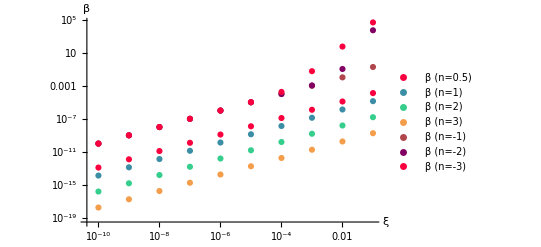

```mathematica
ListLogLogPlot[{ξβ05, ξβ1 ,  ξβ2,  ξβ3, ξβm1 ,  ξβm2,  ξβm3},PlotLegends->{"β (n=0.5)", "β (n=1)","β (n=2)","β (n=3)",  "β (n=-1)","β (n=-2)","β (n=-3)"}, PlotStyle->{RGBColor["#FA003F"],RGBColor["#3B8EA5"],RGBColor["#35CE8D"],RGBColor["#F49E4C"],RGBColor["#B0454C"],  RGBColor["#820263"]},Joined->False,
AxesLabel->{"ξ","β"} ]
```

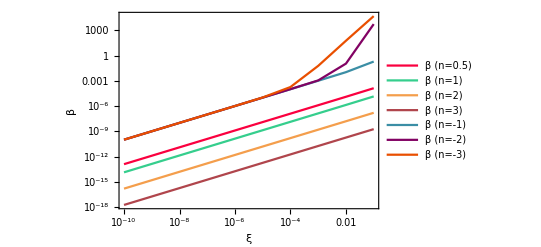

```mathematica
ListLogLogPlot[{ξβ05, ξβ1 ,  ξβ2,  ξβ3, ξβm1 ,  ξβm2,  ξβm3},PlotLegends->{"β (n=0.5)", "β (n=1)","β (n=2)","β (n=3)",  "β (n=-1)","β (n=-2)","β (n=-3)"}, PlotStyle->{RGBColor["#FA003F"],RGBColor["#35CE8D"],RGBColor["#F49E4C"],RGBColor["#B0454C"],  RGBColor["#3B8EA5"], RGBColor["#820263"],  RGBColor["#E94F00"]},Joined->True,
 Frame->True,FrameLabel->{"ξ","β"}, PlotRangePadding->0 , BaseStyle->{FontSize->13} ]
```

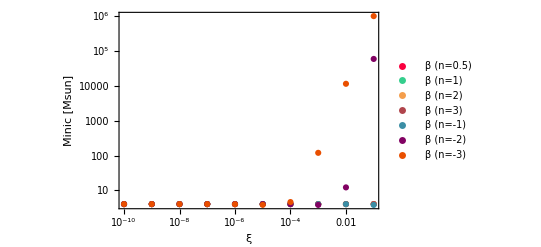

```mathematica
ListLogLogPlot[{ξmass05,ξmass1, ξmass2, ξmass3, ξmassm1, ξmassm2,ξmassm3},PlotLegends->{"β (n=0.5)", "β (n=1)","β (n=2)","β (n=3)",  "β (n=-1)","β (n=-2)","β (n=-3)"}, PlotStyle->{RGBColor["#FA003F"],RGBColor["#35CE8D"],RGBColor["#F49E4C"],RGBColor["#B0454C"],  RGBColor["#3B8EA5"], RGBColor["#820263"],  RGBColor["#E94F00"]},Joined->False,
 Frame->True,FrameLabel->{"ξ","Minic [Msun]"}, PlotRangePadding->0 , BaseStyle->{FontSize->13} ]
```

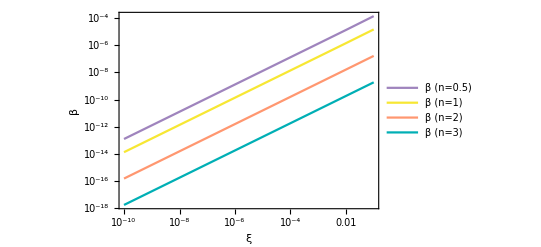

```mathematica
ListLogLogPlot[{ξβ05, ξβ1 ,  ξβ2,  ξβ3},PlotLegends->{"β (n=0.5)", "β (n=1)","β (n=2)","β (n=3)"},Joined->True, PlotStyle->{RGBColor["#9F84BD"],RGBColor["#F7E733"],RGBColor["#FF9770"],RGBColor["#00AFB5"]},
 Frame->True,FrameLabel->{"ξ","β"}, PlotRangePadding->0 , BaseStyle->{FontSize->13}]
```

```mathematica
Export["/home/iara/doctorado/tres incognitas/betanpos.png",%184,"PNG"]
```

/home/iara/doctorado/tres incognitas/betanpos.png

```mathematica
Export["/home/iara/doctorado/tres incognitas/betanpos.png",%178,"PNG"]
```

/home/iara/doctorado/tres incognitas/betanpos.png

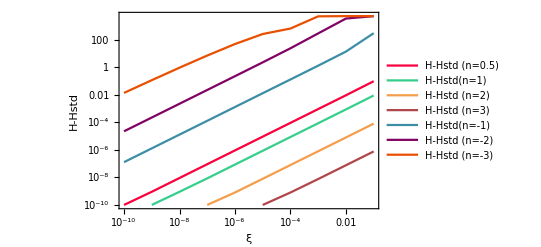

```mathematica
ListLogLogPlot[{restarHstd[ξhubble05], restarHstd[ξhubble1],restarHstd[ξhubble2],restarHstd[ξhubble3], restarHstd[ξhubblem1],restarHstd[ξhubblem2],restarHstd[ξhubblem3]},PlotLegends->{"H-Hstd (n=0.5)", "H-Hstd(n=1)","H-Hstd (n=2)","H-Hstd (n=3)", "H-Hstd(n=-1)","H-Hstd (n=-2)","H-Hstd (n=-3)"},Joined->True, 
PlotStyle->{RGBColor["#FA003F"],RGBColor["#35CE8D"],RGBColor["#F49E4C"],RGBColor["#B0454C"],  RGBColor["#3B8EA5"], RGBColor["#820263"],  RGBColor["#E94F00"]},  Frame->True,FrameLabel->{"ξ","H-Hstd"}, PlotRangePadding->0  , BaseStyle->{FontSize->13}]
```

```mathematica
restarHstd[lista_]:={#[[1]],Abs[#[[2]]-5000.00]}&/@lista;
```

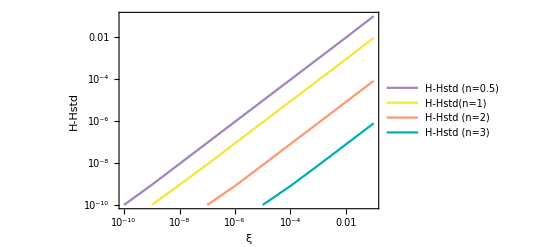

```mathematica
ListLogLogPlot[{restarHstd[ξhubble05], restarHstd[ξhubble1],restarHstd[ξhubble2],restarHstd[ξhubble3]},PlotLegends->{"H-Hstd (n=0.5)", "H-Hstd(n=1)","H-Hstd (n=2)","H-Hstd (n=3)"},Joined->True, 
PlotStyle->{RGBColor["#9F84BD"],RGBColor["#F7E733"],RGBColor["#FF9770"],RGBColor["#00AFB5"]},  Frame->True,FrameLabel->{"ξ","H-Hstd"}, PlotRangePadding->0  , BaseStyle->{FontSize->13}]
```

```mathematica
Export["/home/iara/doctorado/tres incognitas/hubblenpos.png",%186,"PNG"]
```

/home/iara/doctorado/tres incognitas/hubblenpos.png

```mathematica
Export["/home/iara/doctorado/tres incognitas/hubblenpos.png",%177,"PNG"]
```

/home/iara/doctorado/tres incognitas/hubblenpos.png

```mathematica
Show[%174,Axes->True]
```

Show::gtype: Out is not a type of graphics.

Show[%174,Axes→True]

```mathematica
(*1. Extraemos las posiciones ignorando el primer punto*)
xiValores=ξβ05[[2;;,1]];
betaValores=ξβ05[[2;;,2]];
datosColumna={0,#}&/@betaValores;

(*2. Generamos los colores automáticamente para los datos restantes*)
colores=ColorData["BlueGreenYellow"]/@Subdivide[0,1,Length[xiValores]-1];

(*3. Graficamos aislando los puntos*)
graficoMudo=ListLogPlot[List/@datosColumna,PlotStyle->colores,PlotMarkers->{"●",15},Axes->False,Frame->False,Background->None,PlotRange->{{-0.5,0.5},{10^-30,1}}];

Export["puntos_limpios_final05.png",graficoMudo,Background->None, ImageResolution->400]
```

puntos_limpios_final05.png

```mathematica
(*4. Creamos la leyenda separada*)leyenda=PointLegend[colores,Style[StringForm["ξ = ``",ScientificForm[#]],15,Black]&/@xiValores,LegendMarkers->"●",LegendMarkerSize->20,LegendLayout->{"Column",2},Background->None];

Export["leyenda_final.png",leyenda,Background->None, ImageResolution->1000]
```

leyenda_final.png

```mathematica
betaValores
```

{{0.1,0.19247621598034971},{0.01,0.010644061484872569},{0.001,0.0010206742536194404},{0.0001,0.00010165094184122708},{0.00001,0.000010160949023070201},{1.×10^-6,1.0160534929531489×10^-6},{1.×10^-7,1.0160493511955542×10^-7},{1.×10^-8,1.0160489369486202×10^-8},{1.×10^-9,1.01605×10^-9},{1.×10^-10,1.016048891377988×10^-10}}

```mathematica
xiValores
```

{{0.1,0.19247621598034971},{0.01,0.010644061484872569},{0.001,0.0010206742536194404},{0.0001,0.00010165094184122708},{0.00001,0.000010160949023070201},{1.×10^-6,1.0160534929531489×10^-6},{1.×10^-7,1.0160493511955542×10^-7},{1.×10^-8,1.0160489369486202×10^-8},{1.×10^-9,1.01605×10^-9},{1.×10^-10,1.016048891377988×10^-10}}

```mathematica
datosColumna=ξβm2[[2;;, 2]]
xiValores={0,#[[1]]}&/@ξβm2;
```

{0.11044380998525885,0.0011182165639580407,0.00010249775057461475,0.000010169307484080264,1.0161370439989212×10^-6,1.0160577057827187×10^-7,1.0160497718154046×10^-8,1.0160489790266524×10^-9,1.0160488996944×10^-10}

```mathematica
colores=ColorData["BlueGreenYellow"]/@Subdivide[0,1,Length[xiValores]-1];
```

```mathematica
graficoMudo=ListLogPlot[List/@datosColumna,PlotStyle->colores,PlotMarkers->{"●",15},Axes->False,Frame->False,Background->None,PlotRange->{{-0.5,0.5},{10^-30,1}}];
```

```mathematica
Export["puntos_limpios_finalm2.png",graficoMudo,Background->None, ImageResolution->400]
```

puntos_limpios_finalm2.png

```mathematica
(*4. Creamos la leyenda separada*)leyenda=PointLegend[colores,Style[StringForm["ξ = ``",ScientificForm[#]],15,Black]&/@xiValores,LegendMarkers->"●",LegendMarkerSize->20,LegendLayout->{"Column",2},Background->None];
```